```mathematica
SetDirectory[NotebookDirectory[]];
T=100;C0=0.5;C1=1;τ1=0.15;τ2=0.2;τ3=0.9;
(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;maxtime=80;
Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T]-τ3 T)(C0-C1)/(T- τ3 T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,0, True,(C0-C1)/(T- τ3 T)];
```

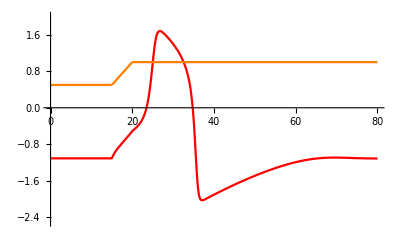

Fig3a.png

```mathematica
(*Look for stable equilibrium*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;

{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.01Min[τ2-τ1,1-τ3]T];
(*Voltage/capacitance plot*)
voltage=Plot[V[t],{t,0,maxtime},PlotRange->{-2.5,2},ColorFunction->Function[{t},Which[Mod[t,2T]<T,Red,True,Default]],ColorFunctionScaling->False,PlotLegends->Placed[StringJoin["C0=",ToString[C0],", C1=",ToString[C1],", T= ",ToString[T],",\n","τ1= ",ToString[τ1],", τ2= ",ToString[τ2],", τ3= ",ToString[τ3],",\n","ε=",ToString[ep],", γ=",ToString[γ],", β=",ToString[β]],Above]];
capacitance=Plot[Ct[t],{t,0,maxtime},PlotPoints->10000,MaxRecursion->3,PlotStyle->Orange];

g1=Show[voltage, capacitance]
Export["Fig3a.png",g1]
```

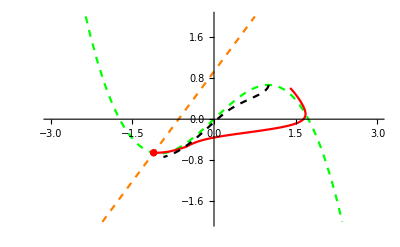

```mathematica
(*Phase plane*)
g1=ParametricPlot[{{V[t],W[t]}},{t,0,30},ColorFunction->Function[{x,y,t},Which[Mod[t,2T]<T,Red,True,Default]],ColorFunctionScaling->False];
g2=Plot[{v-v^3/3,(v+β)/γ},{v,-3,3},PlotRange->{-2,2},PlotStyle->{{Green,Dashed},{Orange,Dashed}}];
g3=ListPlot[{{v0,w0}},PlotStyle->{Red}];
maxtimesep=26.5;
{Vsep,Wsep}=NDSolveValue[{-v'[t]== v[t]-v[t]^3/3-w[t],-w'[t]==ep(v[t]-γ w[t]+β),v[0]==1,w[0]==2/3},{v,w},{t,0,maxtimesep}];
separatrix=ParametricPlot[{Vsep[t],Wsep[t]},{t,0,maxtimesep},PlotStyle->{Black,Dashed}];
Show[g2,g1,g3,separatrix]
```